```mathematica
PotentialSmearing[Cij α/r]
```

(Cij α Erf[r σ])/r

```mathematica
PotentialSmearing[-3/4 Cij(b*r+c)]
```

-(3 Cij (2 r σ ((b ⅇ^(-r^2 σ^2))/(√π)+c √(σ^2))+(b+2 b r^2 σ^2) Erf[r σ]))/(8 r σ^2)

```mathematica
SphericalLaplacian[Cij α/r Erf[σ*r]]//Simplify
```

-(4 Cij ⅇ^(-r^2 σ^2) α σ^3)/(√π)

{{-0.253-0.567656 (5.62837 ⅇ^(-9.25199 r^2)+0.419118 ⅇ^(-1.98379 r^2)+0.0300688 ⅇ^(-0.24366 r^2))-4/3 ((0.25 Erf[0.493619 r])/r+(0.15 Erf[1.40847 r])/r+(0.2 Erf[3.04171 r])/r)+(0.0312255 ⅇ^(-0.15 r) (38.4302 ⅇ^(0.15 r) r+1.00059 (0.15-19.2151 r) Erfc[0.161311 (0.15-19.2151 r)]-ⅇ^(0.0375 (0.0156127+8 r)) (0.15+19.2151 r) Erfc[0.161311 (0.15+19.2151 r)]))/r}}

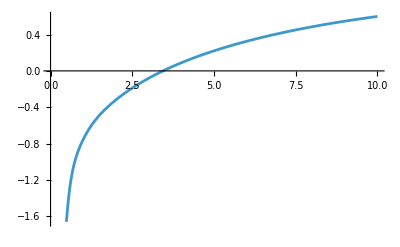

```mathematica
{S,L,J}={0,0,0};
Vij=Potential[{4,4},{S,L,J},"GIScreen"]
Plot[Vij,{r,0,10}]
```

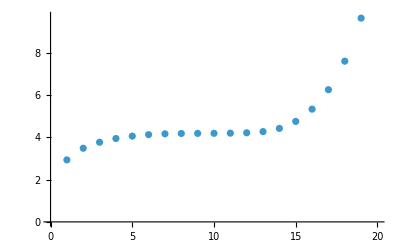

{2.93791,3.48939,3.77325,3.95033,4.06439,4.13465,4.17249,4.18806,4.19368,4.19704,4.20385,4.22236,4.2775,4.42818,4.76129,5.34106,6.26307,7.61377,9.65298,12.5738}

```mathematica
{Nmax,Rmax,Rmin}={20,10,0.1};
{e,v}=MesonGEM[{4,4},{S,L,J},{Nmax,Rmax,Rmin},"GIScreen"];
ListPlot[e]
e
```

```mathematica
GetRMSRadius[1,L,{Nmax,Rmax,Rmin},v]
```

0.30396

```mathematica
GetRMSRadius[2,L,{Nmax,Rmax,Rmin},v]
```

0.755369

```mathematica
GetRMSRadius[3,L,{Nmax,Rmax,Rmin},v]
```

1.25977

```mathematica
GetRMSRadius[4,L,{Nmax,Rmax,Rmin},v]
```

1.85246

0.849903 ⅇ^(-3.89386 r^2)-0.992712 ⅇ^(-2.39802 r^2)+1.57727 ⅇ^(-1.47682 r^2)-0.977113 ⅇ^(-0.909497 r^2)+1.25667 ⅇ^(-0.560112 r^2)-0.467657 ⅇ^(-0.344944 r^2)+0.708733 ⅇ^(-0.212433 r^2)-0.246249 ⅇ^(-0.130827 r^2)+0.235883 ⅇ^(-0.0805693 r^2)-0.132689 ⅇ^(-0.0496184 r^2)+0.0793586 ⅇ^(-0.0305574 r^2)-0.0456133 ⅇ^(-0.0188187 r^2)+0.025358 ⅇ^(-0.0115895 r^2)-0.0135716 ⅇ^(-0.00713736 r^2)+0.00691211 ⅇ^(-0.00439553 r^2)-0.0032757 ⅇ^(-0.00270698 r^2)+0.00138792 ⅇ^(-0.00166709 r^2)-0.000489976 ⅇ^(-0.00102667 r^2)+0.000126216 ⅇ^(-0.000632275 r^2)-0.0000173526 ⅇ^(-0.000389386 r^2)

1.86221

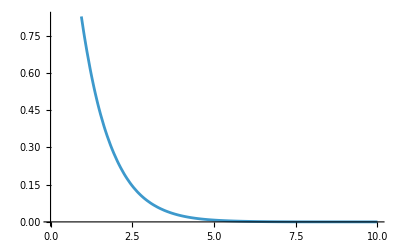

```mathematica
gwv=GetGEMRnlr[1,L,{Nmax,Rmax,Rmin},v]
gwv/.{r->0}
Plot[gwv,{r,0,10}]
```

0.795095

1.06505 ⅇ^(-0.316088 r^2)

1.06505

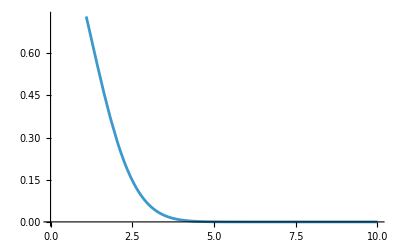

```mathematica
beta=GetSHOBeta[1,L,{Nmax,Rmax,Rmin},v]
swv=GetSHORnlr[1,L,beta]
swv/.{r->0}
Plot[swv,{r,0,10}]
```